# Il tappeto di Serpinskij

```mathematica
origin = {{0,0}};
e1={1,0};
e2={0,1};
```

```mathematica
tappeto[p_]:=
Flatten[
Delete[
Table[3p+i e1+j e2,{i,0,2},{j,0,2}]
,{2,2}]
,1]
```

```mathematica
tappeto2[list_]:=Flatten[Map[tappeto,list],1]
```

```mathematica
tappeto3[n_]:=Nest[tappeto2,origin,n]
```

```mathematica
tappetoDraw[n_]:=GraphicsRow[
Table[
Graphics[
Map[Rectangle,tappeto3[i]]]
,{i,n}]]
```

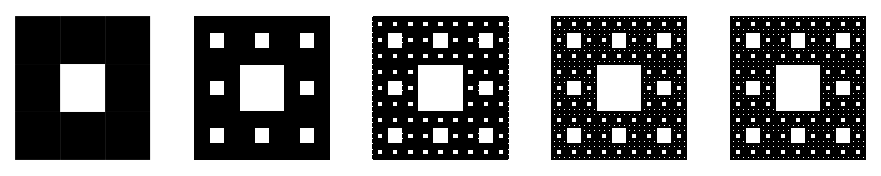

```mathematica
tappetoDraw[5]
```

```mathematica
￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿￿
```